# Finite Temperature Physics of Full Model

Isaac Wang

This notebook compute the finite temperature effective potential of the full model as well as the phase transition quantities.

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,{S,β}∈Reals};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24537+2.46099 ⅈ and 0.000286423 for the integral and error estimates.

## Effective Potential

```mathematica
Clear[JBfit,JFfit]
```

```mathematica
Jbdata=Import[NotebookDirectory[]<>"finiteT_b.dat.txt","Table"];
Jfdata=Import[NotebookDirectory[]<>"finiteT_f.dat.txt","Table"];
JBfit[x_]=Interpolation[Jbdata][x];
JFfit[x_]=Interpolation[Jfdata][x];
```

```mathematica
JFfit[1]
```

-1.56732

```mathematica
V0[h_,S_]:=-1/2(μHsq-A f Cos[δ]) h^2+1/4 λ h^4-1/2 A f (h^2-2 v^2)Cos[S/f-δ]-f^2 μSsq (Cos[S/f]-1);
mWsq[h_]=1/4 g2mZ^2 h^2;
mZsq[h_]=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]=1/2 ytmZ^2 h^2;
mWL[h_,T_]=1/4 g2mZ^2 h^2+11/6 g2mZ^2 T^2;
mgauge=({{g2mZ^2 x1^2/4+11/6 g2mZ^2 x2^2, -g2mZ g1mZ x1^2/4}, {-g2mZ g1mZ x1^2/4, g1mZ^2 x1^2/4+11/6 g1mZ^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mBL[h_,T_]=gaugeL[[1]]/.{x1->h,x2->T};
mZL[h_,T_]=gaugeL[[2]]/.{x1->h,x2->T};
mgs[h_,S_,T_]:=λ h^2-μHsq+A f Cos[δ]-A f Cos[S/f-δ]+T^2(1/2 λ+ytmZ^2/4+3/16 g2mZ^2+1/16 g1mZ^2);
mscalar={{3λ h^2-μHsq+A f Cos[δ]-A f Cos[S/f-δ]+T^2(1/2 λ+ytmZ^2/4+3/16 g2mZ^2+1/16 g1mZ^2),A h Sin[S/f-δ]},{A h Sin[S/f-δ],A (h^2-2 v^2)Cos[S/f-δ]/(2f)+μSsq Cos[S/f]}};
mhsq[h_,S_,T_]=Eigenvalues[mscalar][[2]]//Simplify;
mSsq[h_,S_,T_]=Eigenvalues[mscalar][[1]]//Simplify;
(*VCW[h_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));*)
VCW[h_,S_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)+3 mgs[h,S,T]^2(Log[mgs[h,S,T]/mZ^2]-3/2)+mhsq[h,S,T]^2(Log[mhsq[h,S,T]/mZ^2]-3/2)+mSsq[h,S,T]^2(Log[mSsq[h,S,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2))//Re;
VCW‵0T[h_,S_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)+3 mgs[h,S,0]^2(Log[mgs[h,S,0]/mZ^2]-3/2)+mhsq[h,S,0]^2(Log[mhsq[h,S,0]/mZ^2]-3/2)+mSsq[h,S,0]^2(Log[mSsq[h,S,0]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2))//Re;
V0T[h_,S_]:=V0[h,S]+VCW‵0T[h,S];
(*VFT[h_,T_]:=T^4/(2 π^2)(4JBBes[mWsq[h]/T^2]+2JBBes[mZsq[h]/T^2]+2JBBes[mWL[h,T]/T^2]+JBBes[mZL[h,T]/mZ^2]+JBBes[mBL[h,T]/mZ^2]-12JFBes[mtsq[h]/T^2]);*)
VFT[h_,S_,T_]:=T^4/(2 π^2)(4JBfit[mWsq[h]/T^2]+2JBfit[mWL[h,T]/T^2]+2JBfit[mZsq[h]/T^2]+JBfit[mZL[h,T]/T^2]+JBfit[mBL[h,T]/T^2]+3JBfit[mgs[h,S,T]/T^2]+JBfit[mhsq[h,S,T]/T^2]+JBfit[mSsq[h,S,T]/T^2]+12JFfit[mtsq[h]/T^2]);
Vtot[h_,S_,T_]:=V0[h,S]+VCW[h,S,T]+VFT[h,S,T];
```

## Benchmark

```mathematica
num={λ->0.1495054660591447,A->6.690393908229027,f->3168,δ->(2π)/5,μHsq->8765.524609336542,μSsq->182.51632189049914,v->vnum/(√2)}(*mS=5,sinθ=0.1*)
```

{λ→0.149505,A→6.69039,f→3168,δ→(2 π)/5,μ_H^2→8765.52,μ_S^2→182.516,v→174.104}

```mathematica
V0Tnum[h_,S_]=V0T[h,S]/.num;
Vtotnum[h_,S_,T_]=Vtot[h,S,T]/.num;
```

```mathematica
minSdata=Table[{h,T,
sol=Minimize[{Vtotnum[h,S,T],-3168<S<3168},S][[2]];
S/.sol},{h,0.1,290,20},{T,20,100,10}];
minSdataform=Flatten[minSdata,1];
Spath[h_,T_]=Interpolation[minSdataform][h,T]
Vtot1d[h_,T_]:=Vtotnum[h,Spath[h,T],T]
```

InterpolatingFunction[…](h,T)

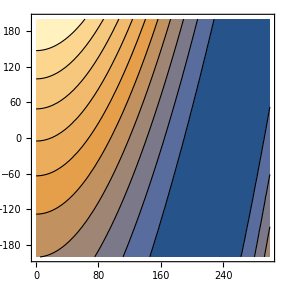

```mathematica
ContourPlot[V0Tnum[h,S],{h,0,300},{S,-200,200},Contours->10,PlotRange->Full]
```

```mathematica
FindRoot[D[V0Tnum[h,S],{{h,S}}]==0,{{h,vnum},{S,0}}]
```

{h→248.18,S→10.8663}

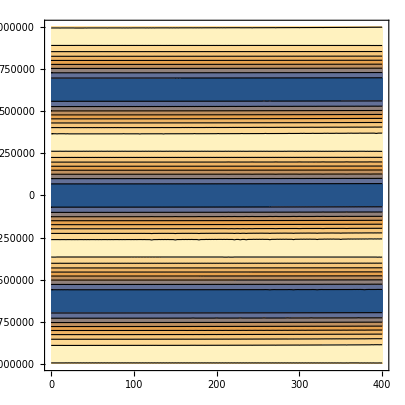

```mathematica
ContourPlot[V0Tnum[h,S],{h,0,400},{S,-10^6,10^6}]
```

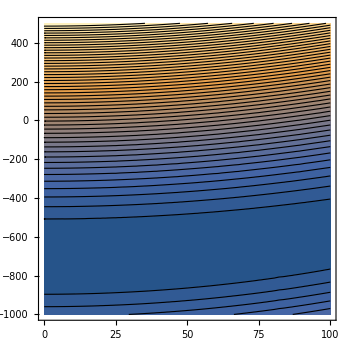

```mathematica
ContourPlot[Vtotnum[h,S,70],{h,0,100},{S,-1000,500},Contours->50]
```

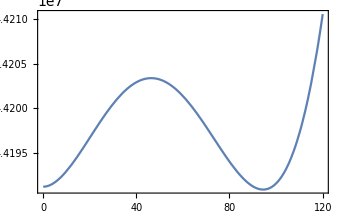

```mathematica
Ttest=63.301;
Plot[Vtot1d[h,Ttest],{h,0.1,120}]
```

```mathematica
vc=h/.NMinimize[{Vtot1d[h,Ttest],h>50},h][[2]]
vc/Ttest
```

94.4399

1.49192

```mathematica
Smin0=S/.NMinimize[{Vtotnum[10^-5,S,Ttest],-3180<S<3180},S][[2]]
```

-1113.38

```mathematica
mhsq[10^-5,Smin0,Ttest]/.num
(mhsq[10^-5,Smin0,Ttest]/.num)/Ttest^2
```

181.941

0.0454056

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ND[Vtot1d[h,Ttest],{h,2},vc]
ND[Vtot1d[h,Ttest],{h,2},vc]/Ttest^2
```

38.7335

0.00966367

```mathematica
num={λ->0.1495054660591447,A->6.690393908229027,f->31680,δ->(2π)/5,μHsq->8765.524609336542,μSsq->182.51632189049914,v->vnum/(√2)}(*mS=5,sinθ=0.1*)
V0Tnum[h_,S_]=V0T[h,S]/.num;
Vtotnum[h_,S_,T_]=Vtot[h,S,T]/.num;
```

{λ→0.149505,A→6.69039,f→31680,δ→(2 π)/5,μ_H^2→8765.52,μ_S^2→182.516,v→174.104}

```mathematica
minSdata=Table[{h,T,
sol=Minimize[{Vtotnum[h,S,T],-31680<S<31680},S][[2]];
S/.sol},{h,0.1,290,20},{T,20,100,10}];
minSdataform=Flatten[minSdata,1];
Spath[h_,T_]=Interpolation[minSdataform][h,T]
Vtot1d[h_,T_]:=Vtotnum[h,Spath[h,T],T]
```

InterpolatingFunction[…](h,T)

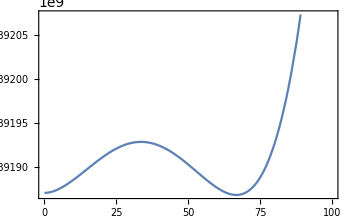

```mathematica
Ttest=76.447;
Plot[Vtot1d[h,Ttest],{h,0.1,100}]
```

```mathematica
vc=h/.NMinimize[{Vtot1d[h,Ttest],h>50},h][[2]]
vc/Ttest
```

66.7061

0.87258

```mathematica
Smin0=S/.NMinimize[{Vtotnum[10^-5,S,Ttest],-31800<S<31800},S][[2]]
```

-1039.43

```mathematica
mhsq[10^-5,Smin0,Ttest]/.num
(mhsq[10^-5,Smin0,Ttest]/.num)/Ttest^2
```

227.095

0.0388586

### 2-loop thermal mass

```mathematica
V0[h_,S_]:=-1/2(μHsq-A f Cos[δ]) h^2+1/4 λ h^4-1/2 A f (h^2-2 v^2)Cos[S/f-δ]-f^2 μSsq (Cos[S/f]-1);
mWsq[h_]=1/4 g2mZ^2 h^2;
mZsq[h_]=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]=1/2 ytmZ^2 h^2;
mWL[h_,T_]=1/4 g2mZ^2 h^2+11/6 g2mZ^2 T^2;
mgauge=({{g2mZ^2 x1^2/4+11/6 g2mZ^2 x2^2, -g2mZ g1mZ x1^2/4}, {-g2mZ g1mZ x1^2/4, g1mZ^2 x1^2/4+11/6 g1mZ^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mBL[h_,T_]=gaugeL[[1]]/.{x1->h,x2->T};
mZL[h_,T_]=gaugeL[[2]]/.{x1->h,x2->T};
mgs[h_,S_,T_]:=λ h^2-μHsq+A f Cos[δ]-A f Cos[S/f-δ]+T^2(1/2 λ+ytmZ^2/4+3/16 g2mZ^2+1/16 g1mZ^2)+μHsq (0.005352596257869273-0.14847164860924716 λ)+Log[mZ^2/T^2] (T^2 (0.019605366079896464-0.024807959183828495 λ)+(0.037995443865876666λ+0.011517183612837304) μHsq)+(0.091486875828001 λ^2+0.054563765959103276λ-0.03159064255588816) T^2;
mh2loop=μHsq (0.005352596257869273-0.14847164860924716 λ)+Log[mZ^2/T^2] (T^2 (0.019605366079896464-0.024807959183828495 λ)+(0.037995443865876666λ+0.011517183612837304) μHsq)+(0.091486875828001 λ^2+0.054563765959103276λ-0.03159064255588816) T^2;
mscalar={{3λ h^2-μHsq+A f Cos[δ]-A f Cos[S/f-δ]+T^2(1/2 λ+ytmZ^2/4+3/16 g2mZ^2+1/16 g1mZ^2)+mh2loop,A h Sin[S/f-δ]},{A h Sin[S/f-δ],A (h^2-2 v^2)Cos[S/f-δ]/(2f)+μSsq Cos[S/f]}};
mhsq[h_,S_,T_]=Eigenvalues[mscalar][[2]]//Simplify;
mSsq[h_,S_,T_]=Eigenvalues[mscalar][[1]]//Simplify;
(*VCW[h_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));*)
VCW[h_,S_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)+3 mgs[h,S,T]^2(Log[mgs[h,S,T]/mZ^2]-3/2)+mhsq[h,S,T]^2(Log[mhsq[h,S,T]/mZ^2]-3/2)+mSsq[h,S,T]^2(Log[mSsq[h,S,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2))//Re;
VFT[h_,S_,T_]:=T^4/(2 π^2)(4JBfit[mWsq[h]/T^2]+2JBfit[mWL[h,T]/T^2]+2JBfit[mZsq[h]/T^2]+JBfit[mZL[h,T]/T^2]+JBfit[mBL[h,T]/T^2]+3JBfit[mgs[h,S,T]/T^2]+JBfit[mhsq[h,S,T]/T^2]+JBfit[mSsq[h,S,T]/T^2]+12JFfit[mtsq[h]/T^2]);
Vtot[h_,S_,T_]:=V0[h,S]+VCW[h,S,T]+VFT[h,S,T];
```

```mathematica
num={λ->0.1495054660591447,A->6.690393908229027,f->3168,δ->(2π)/5,μHsq->8765.524609336542,μSsq->182.51632189049914,v->vnum/(√2)}(*mS=5,sinθ=0.1*)
```

{λ→0.149505,A→6.69039,f→3168,δ→(2 π)/5,μ_H^2→8765.52,μ_S^2→182.516,v→174.104}

```mathematica
Vtotnum[h_,S_,T_]=Vtot[h,S,T]/.num;
```

```mathematica
minSdata=Table[{h,T,
sol=Minimize[{Vtotnum[h,S,T],-3168<S<3168},S][[2]];
S/.sol},{h,0.1,150,20},{T,20,100,10}];
minSdataform=Flatten[minSdata,1];
Spath[h_,T_]=Interpolation[minSdataform][h,T]
Vtot1d[h_,T_]:=Vtotnum[h,Spath[h,T],T]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction[…](h,T)

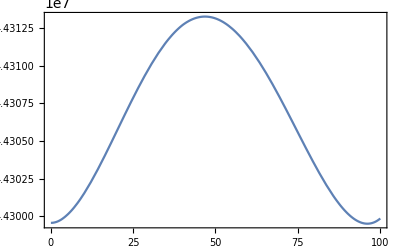

```mathematica
Ttest=63.246;
Plot[Vtot1d[h,Ttest],{h,0.1,100}]
```

```mathematica
vc=h/.NMinimize[{Vtot1d[h,Ttest],h>60},h][[2]]
vc/Ttest
mh2loop/.num/.T->Ttest
```

96.0838

1.51921

-76.3629

```mathematica
num={λ->0.1495054660591447,A->6.690393908229027,f->31680,δ->(2π)/5,μHsq->8765.524609336542,μSsq->182.51632189049914,v->vnum/(√2)}(*mS=5,sinθ=0.1*)
Vtotnum[h_,S_,T_]=Vtot[h,S,T]/.num;
```

{λ→0.149505,A→6.69039,f→31680,δ→(2 π)/5,μ_H^2→8765.52,μ_S^2→182.516,v→174.104}

```mathematica
minSdata=Table[{h,T,
sol=Minimize[{Vtotnum[h,S,T],-31680<S<31680},S][[2]];
S/.sol},{h,0.1,150,20},{T,20,100,10}];
minSdataform=Flatten[minSdata,1];
Spath[h_,T_]=Interpolation[minSdataform][h,T]
Vtot1d[h_,T_]:=Vtotnum[h,Spath[h,T],T]
```

InterpolatingFunction[…](h,T)

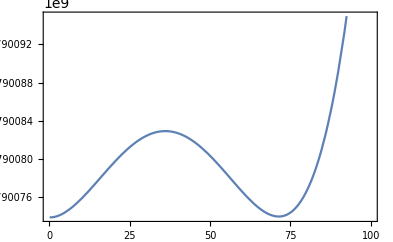

```mathematica
Ttest=76.23;
Plot[Vtot1d[h,Ttest],{h,0.1,100}]
```

```mathematica
vc=h/.NMinimize[{Vtot1d[h,Ttest],h>60},h][[2]]
vc/Ttest
mh2loop/.num/.T->Ttest
```

71.3509

0.935995

-184.823

For larger f, the modification is more significant.
c=3: 1.49->1.51.
c=30: 0.86->0.94